```mathematica
RK45[f_,t0_,T_,h0_,tol_,y0_]:=Module[{
a=N@{0,1/4,3/8,12/13,1,1/2},
b=N@{
{0,0,0,0,0,0},
{1/4,0,0,0,0,0},
{3/32,9/32,0,0,0,0},
{1932/2197,-7200/2197,7296/2197,0,0,0},
{439/216,-8,3680/513,-845/4104,0,0},
{-8/27,2,-3544/2565,1859/4104,-11/40,0}
},
p=N@{{16/135,0,6656/12825,28561/56430,-9/50,2/55},{25/216,0,1408/2565,2197/4104,-1/5,0}},
y={y0},t={t0},err={0},
tc=t0,yc=y0,hc=h0,
k,s,errc,hnext
},

While[T≥tc,
k=ConstantArray[0,6];
For[s=1,s≤6,s++,
k⟦s⟧=hc f[tc+a⟦s⟧hc,yc+b⟦s⟧.k];
];
errc=(p⟦1⟧-p⟦2⟧).k;
hnext=hc (tol/Abs[errc])^(1/5);
If[Abs@errc>tol,hc=hnext;Continue[],0];
yc+=p⟦1⟧.k;
AppendTo[y,yc];
tc+=hc;
AppendTo[t,tc];
AppendTo[err,errc];
hc=hnext;
];

{t,y,err}
]
```

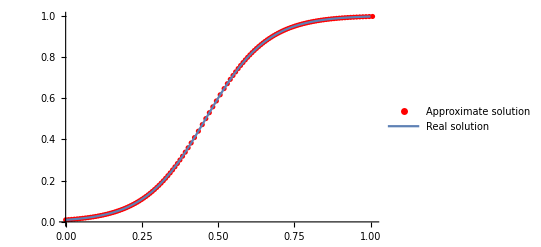

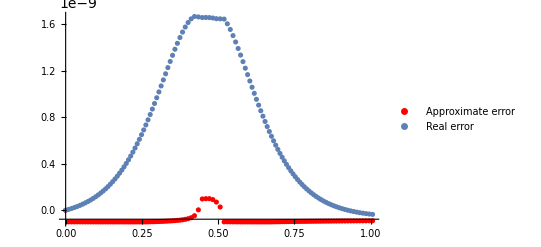

```mathematica
(* Task 2 *)
f[t_,y_]:=10y(1-y);
yr[t_]:=0.01/(0.01+0.99Exp[-10t]);
T=1;
x0=0;
y0=0.01;
h0=0.01;
tol=10^-10;

{x,y,err}=RK45[f,x0,T,h0,tol,y0];
n=Length@x;

approxSol=ListPlot[Thread[{x,y}],PlotStyle->Red,PlotLegends->{"Approximate solution"}];
realSol=Plot[yr[t],{t,x0,T},PlotLegends->{"Real solution"}];
Show[approxSol,realSol]
approxError=ListPlot[Thread[{x,err}],PlotStyle->Red,PlotLegends->{"Approximate error"}];
realError=ListPlot[Table[{x⟦k⟧,yr[x⟦k⟧]-y⟦k⟧},{k,1,n}],PlotLegends->{"Real error"}];
Show[approxError,realError,PlotRange->All]
```

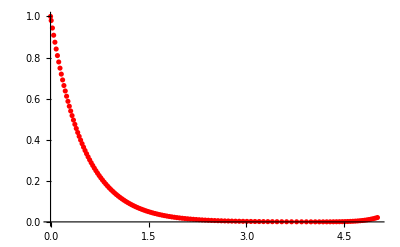

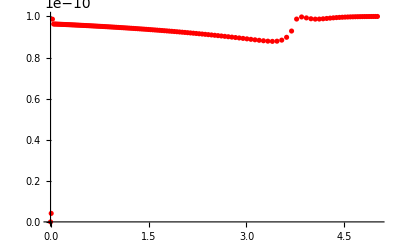

```mathematica
(* Task 3 *)
g[t_,u_]:=-2*u+Exp[-2*(t-6)^2];
t0=0;
u0=1;
T3=5;

{v,u,e3}=RK45[g,t0,T3,h0,tol,u0];

ListPlot[Thread[{v,u}],PlotStyle->Red]
ListPlot[Thread[{v,e3}],PlotStyle->Red]
```